### Analytic solution of the bound state

For the approximate potential V_k=-V_0R, the real space eigenfunction is defined by the following integral.

ψ(x)=(V_0 R)/π ψ(x=0)∫_0^a (Cos(kx))/(k^σ+|E|)dk

where a=∞ for continuous model, a=π for discrete model.

#### Integration by parts

∫_0^a (Cos(kx))/(k^σ+|E|)dk=1/x(Sin(kx))/(k^σ+|E|)|_0^a+1/x∫_0^a Sin(k x)(k^(-1+σ) σ)/((e+k^σ)^2)dk=1/x(Sin(a x))/(a^σ+|E|)+1/x^2 Cos(k x)(k^(-1+σ) σ)/((e+k^σ)^2)|_0^a-1/x^2∫_0^a Cos(k x)((k^(-2+σ) (-1+σ) σ)/((e+k^σ)^2)-(2 k^(-2+2 σ) σ^2)/((e+k^σ)^3))dk

```mathematica
D[1/(k^σ+e),k]
```

-(k^(-1+σ) σ)/((e+k^σ)^2)

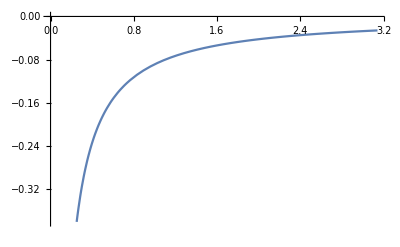

```mathematica
Plot[-(k^(-1+σ) σ)/((e+k^σ)^2)/.{σ-> 0.2,e-> 0.5},{k,0,π}]
```

```mathematica
D[(k^(-1+σ) σ)/((e+k^σ)^2),k]
```

(k^(-2+σ) (-1+σ) σ)/((e+k^σ)^2)-(2 k^(-2+2 σ) σ^2)/((e+k^σ)^3)

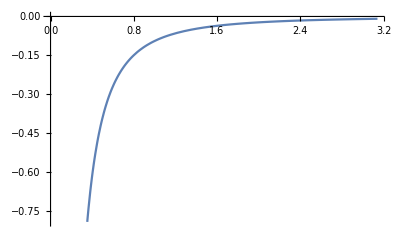

```mathematica
Plot[((k^(-2+σ) (-1+σ) σ)/((e+k^σ)^2)-(2 k^(-2+2 σ) σ^2)/((e+k^σ)^3))/.{σ-> 0.2,e-> 0.5},{k,0,π}]
```

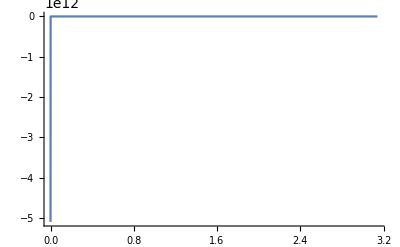

```mathematica
Plot[((k^(-2+σ) (-1+σ) σ)/((e+k^σ)^2)-(2 k^(-2+2 σ) σ^2)/((e+k^σ)^3))/.{σ-> 0.2,e-> 0.5},{k,0,π},PlotRange-> All]
```

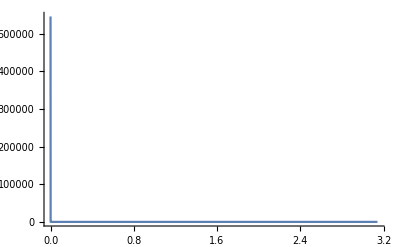

```mathematica
Plot[((k^(-2+σ) (-1+σ) σ)/((e+k^σ)^2)-(2 k^(-2+2 σ) σ^2)/((e+k^σ)^3))/.{σ-> 1.2,e-> 0.5},{k,0,π},PlotRange-> All]
```

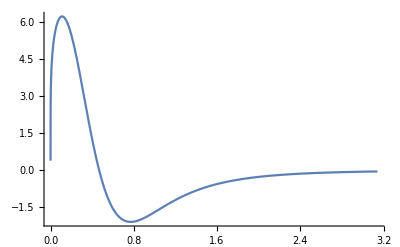

```mathematica
Plot[((k^(-2+σ) (-1+σ) σ)/((e+k^σ)^2)-(2 k^(-2+2 σ) σ^2)/((e+k^σ)^3))/.{σ-> 2.2,e-> 0.5},{k,0,π},PlotRange-> All]
```

When σ<2, the integrand on the right has singularity at k=0.

when x→ ∞, the integrand in the last term is bounded, so it converges to zero as proportional to 1/x^2. So

∫_0^a (Cos(kx))/(k^σ+|E|)dk~1/x(Sin(a x))/(a^σ+|E|)+1/x^2 Cos(k x)(k^(-1+σ) σ)/((e+k^σ)^2)|_0^a=1/x(Sin(a x))/(a^σ+|E|)+1/x^2 Cos(a x)(a^(-1+σ) σ)/((e+a^σ)^2)

```mathematica
f[x_,σ_,a_,e_]:=1/x Sin[a x]/(a^σ + e)+1/x^2(σ a^(σ-1) Cos[a x])/((a^σ + e)^2) ;
g[x_,σ_,a_,e_]:=1/x Sin[a x]/(a^σ + e);
```

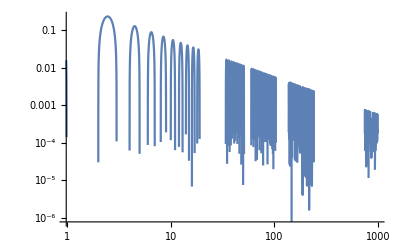

```mathematica
LogLogPlot[f[x,0.2,π,0.5],{x,0,1000}]
```

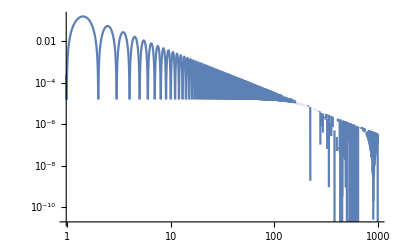

```mathematica
LogLogPlot[f[x,0.2,π,0.5]^2,{x,0,1000}]
```

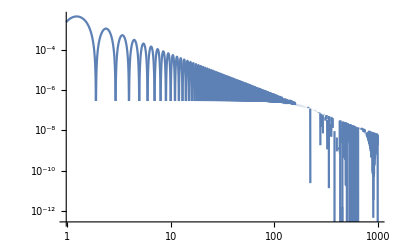

```mathematica
LogLogPlot[f[x,2.2,π,0.5]^2,{x,0,1000}]
```

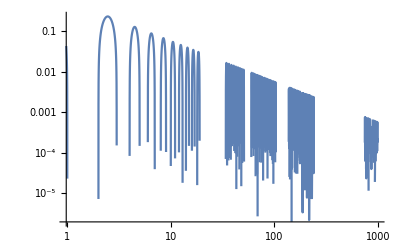

```mathematica
LogLogPlot[g[x,0.2,π,0.5],{x,0,1000}]
```

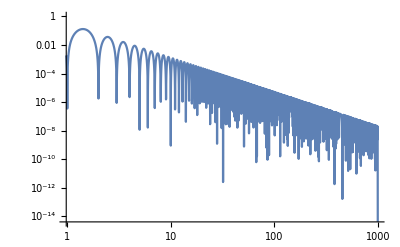

```mathematica
LogLogPlot[g[x,0.2,π,0.5]^2,{x,0,1000}]
```

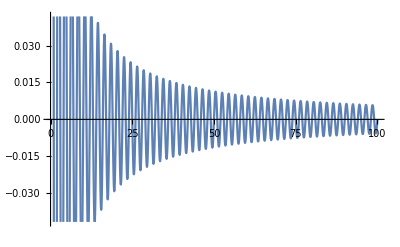

```mathematica
Plot[f[x,0.2,π,0.5],{x,0,100}]
```

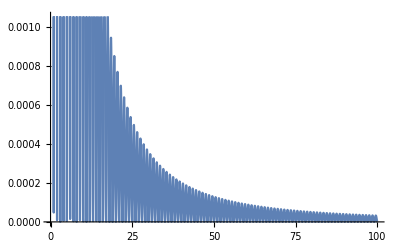

```mathematica
Plot[f[x,0.2,π,0.5]^2,{x,0,100}]
```

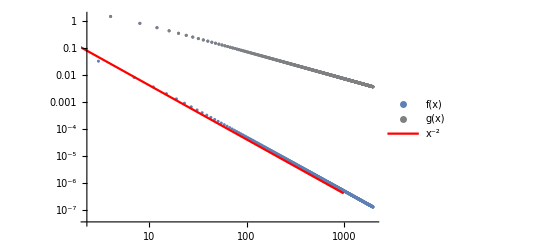

```mathematica
L=2000;
z=(1+0.2);
Show[ListLogLogPlot[8*Table[f[x,0.2,π,1],{x,1,1000,0.5}],PlotLegends->{"f(x)"}],ListLogLogPlot[8*Table[g[x,0.2,π,1],{x,1,1000,0.5}],PlotStyle->Gray,PlotLegends->{"g(x)"}],LogLogPlot[0.4/x^2,{x,1,L/2},PlotStyle->Red,PlotLegends->{"x^-2"}]]
```

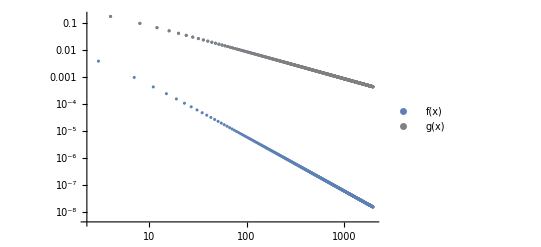

```mathematica
Show[ListLogLogPlot[Table[f[x,0.2,π,1],{x,1,1000,0.5}],PlotLegends->{"f(x)"}],ListLogLogPlot[Table[g[x,0.2,π,1],{x,1,1000,0.5}],PlotStyle->Gray,PlotLegends->{"g(x)"}]]
```